```mathematica
μ = π/4; ϵ = 1;
```

-Graphics-

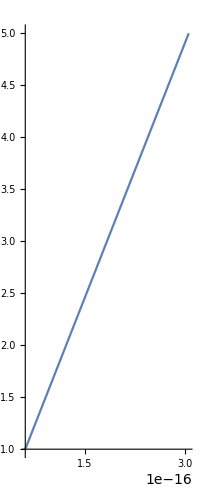

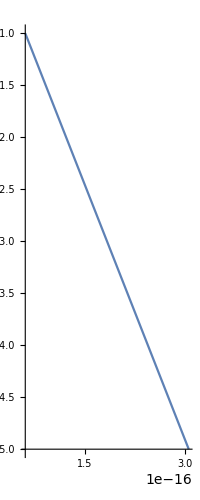

```mathematica
p1=ParametricPlot[{Re[ϵ Exp[ⅈ ϕ]],Im[ϵ Exp[ⅈ ϕ]]},{ϕ,-μ,μ},PlotTheme->"Minimal",PlotStyle->Gray,PlotLegends->{"C_1(ϵ,μ)"}];
p2=ParametricPlot[{Re[r Exp[ⅈ μ]],Im[r Exp[ⅈ μ]]},{r,ϵ,2ϵ},PlotLegends->{"C_2(ϵ,μ)"}];
p3=ParametricPlot[{Re[r Exp[-ⅈ μ]],Im[r Exp[-ⅈ μ]]},{r,ϵ,2ϵ}];
Rasterize[Show[p1,p2,p3,PlotRange->All]]
```